```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

workingdirectory="/home/kirscher/kette_repo/sim_par/nucleus/3N/hyperradial";
SetDirectory[workingdirectory];
matrixfilename="MATOUTB"
```

MATOUTB

```mathematica
normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)])}]
decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[{(Transpose[Oμ].ham).Oμ,(Transpose[Oμ].norm).Oμ}];];
```

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
HNc={};HNuc={};
thr=10^-22;

str=OpenRead[matrixfilename,BinaryFormat->True];
headmarker=BinaryRead[str,"Integer32",ByteOrdering->$ByteOrdering];
NormHamMat=BinaryReadList[str,"Real64",ByteOrdering->$ByteOrdering];
JbasisDim=IntegerPart[Sqrt[Length[NormHamMat]*0.5]];
Close[str];

norm=ArrayReshape[NormHamMat[[1;;JbasisDim^2]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+1;;]],{JbasisDim,JbasisDim}];
decompose[thr,norm,ham];

evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
  renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

evn=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];

Print["Condition number ℕ_ij = ",Max[Abs[evn]]/Min[Abs[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-2;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-2;;]]];

thh=100;(*Max[Abs[λs]];*)
HNc=evn;
HNuc=evhamunnorm;

(*Grid[{{"ev(⟨i|j⟩)\n","ev(⟨i|H_nucl|j⟩)","ev(⟨α|H_nucl|β⟩) ev(𝟙) > "ScientificForm[thr]},{Sort[evn,Re[#1]>Re[#2]&]//MatrixForm,Sort[Eigenvalues[{ham,norm}],R~e[#1]>Re[#2]&]//MatrixForm,Sort[λs,Re[#1]>Re[#2]&]//MatrixForm}}]*)
```

Condition number ℕ_ij = 1.60381×10^16

EV_full(ℍ) = {0.32767,-8.30593}

EV_(EV (𝟙) > threshold)(ℍ) = {0.327411,-8.30741}

```mathematica
HNc
```

{19.7543,6.72775,2.93255,2.06249,1.69563,0.92459,0.418905,0.231937,0.145244,0.0470119,0.0283563,0.0234201,0.00369112,0.0028992,0.00068428,0.000458821,0.00005389,0.0000170799,0.0000112121,1.6307×10^-6,1.42218×10^-6,1.34847×10^-7,4.86447×10^-8,4.20272×10^-9,1.82162×10^-9,1.47973×10^-10,2.95219×10^-11,2.31648×10^-12,1.68057×10^-12,9.45304×10^-13,1.78653×10^-13,5.35698×10^-14,2.4546×10^-14,3.93615×10^-15,1.23171×10^-15}

```mathematica
data1=Select[Re[HNuc],Abs[#]<thh&];data2=Select[Re[HNc],Abs[#]<thh&];
```

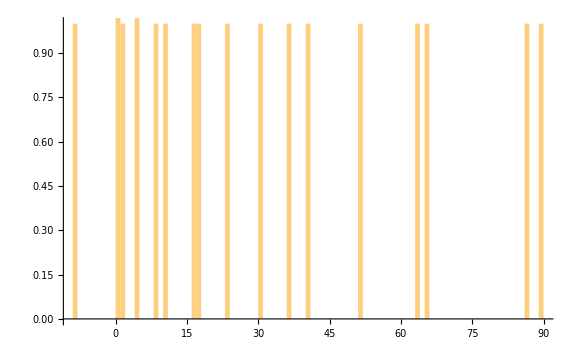

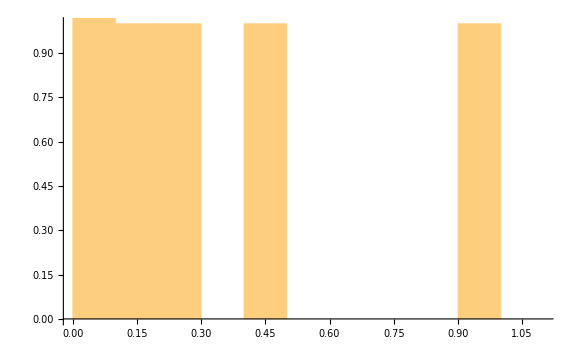

```mathematica
Histogram[data1,{1},PlotRange->{Automatic,{0,1}},ImageSize->Large]
Histogram[data2,{.1},PlotRange->{Automatic,{0,1}},ImageSize->Large]
```

```mathematica
norm//MatrixForm
```

(1. | 0.986986 | 0.942026 | 0.775969 | 0.728877 | 0.689695 | 0.585041 | 0.581508 | 0.535183 | 0.478624 | 0.294752 | 0.244705 | 0.236876 | 0.153424 | 0.0835693 | 0.0718614 | 0.00423343 | 0.00232207 | -0.635134 | -0.526737 | -0.43217 | -0.419052 | -0.417103 | -0.384098 | -0.349504 | -0.272916 | -0.236942 | -0.124239 | -0.119968 | -0.107337 | -0.106736 | -0.0949416 | -0.0810092 | -0.0758889 | -0.0357039
0.986986 | 1. | 0.983108 | 0.857046 | 0.814862 | 0.77842 | 0.676076 | 0.672506 | 0.625078 | 0.565656 | 0.361825 | 0.303618 | 0.294406 | 0.194362 | 0.107822 | 0.0930376 | 0.00563323 | 0.00309484 | -0.663573 | -0.576875 | -0.488592 | -0.47574 | -0.47382 | -0.440866 | -0.405489 | -0.324266 | -0.284761 | -0.155202 | -0.150109 | -0.134959 | -0.134235 | -0.119965 | -0.102955 | -0.0966599 | -0.0463659
0.942026 | 0.983108 | 1. | 0.932469 | 0.899749 | 0.86957 | 0.777639 | 0.774271 | 0.728625 | 0.669241 | 0.449397 | 0.382379 | 0.371604 | 0.251566 | 0.143003 | 0.12397 | 0.00779343 | 0.00429124 | -0.680975 | -0.625037 | -0.549439 | -0.537628 | -0.535849 | -0.504747 | -0.470245 | -0.387073 | -0.344737 | -0.197299 | -0.191221 | -0.173009 | -0.172134 | -0.154781 | -0.133845 | -0.126026 | -0.062036
0.775969 | 0.857046 | 0.932469 | 1. | 0.996231 | 0.987713 | 0.943038 | 0.940991 | 0.910943 | 0.866065 | 0.653167 | 0.575096 | 0.561985 | 0.40523 | 0.245331 | 0.215296 | 0.0149886 | 0.00830546 | -0.66306 | -0.680064 | -0.645815 | -0.638507 | -0.637371 | -0.616185 | -0.590024 | -0.517181 | -0.475286 | -0.304667 | -0.296765 | -0.272635 | -0.271458 | -0.247785 | -0.218337 | -0.207078 | -0.108932
0.728877 | 0.814862 | 0.899749 | 0.996231 | 1. | 0.997524 | 0.967713 | 0.96613 | 0.941879 | 0.903276 | 0.701995 | 0.623725 | 0.610407 | 0.447726 | 0.275826 | 0.242892 | 0.0174163 | 0.00966895 | -0.649086 | -0.683075 | -0.660484 | -0.6546 | -0.653672 | -0.63583 | -0.612809 | -0.545327 | -0.505002 | -0.333093 | -0.324876 | -0.299653 | -0.298418 | -0.273473 | -0.24218 | -0.230138 | -0.123287
0.689695 | 0.77842 | 0.86957 | 0.987713 | 0.997524 | 1. | 0.98284 | 0.981664 | 0.962577 | 0.92977 | 0.740949 | 0.663407 | 0.650054 | 0.483786 | 0.302536 | 0.267205 | 0.0196599 | 0.0109328 | -0.635336 | -0.682665 | -0.669819 | -0.665165 | -0.664416 | -0.64951 | -0.629318 | -0.566969 | -0.52835 | -0.356838 | -0.348414 | -0.32244 | -0.321164 | -0.295297 | -0.262613 | -0.249967 | -0.136009
0.585041 | 0.676076 | 0.777639 | 0.943038 | 0.967713 | 0.98284 | 1. | 0.99998 | 0.995912 | 0.98084 | 0.83774 | 0.766432 | 0.753666 | 0.584623 | 0.381791 | 0.340144 | 0.0270266 | 0.0151065 | -0.58976 | -0.669412 | -0.682746 | -0.681562 | -0.681325 | -0.674905 | -0.663195 | -0.61749 | -0.585215 | -0.421581 | -0.41287 | -0.385655 | -0.384304 | -0.356649 | -0.320957 | -0.306923 | -0.174613
0.581508 | 0.672506 | 0.774271 | 0.940991 | 0.96613 | 0.981664 | 0.99998 | 1. | 0.996464 | 0.982042 | 0.840805 | 0.769827 | 0.757099 | 0.588161 | 0.384707 | 0.342851 | 0.0273196 | 0.0152733 | -0.587999 | -0.668656 | -0.682876 | -0.681814 | -0.681595 | -0.675477 | -0.664076 | -0.619009 | -0.586994 | -0.423812 | -0.415099 | -0.387864 | -0.386511 | -0.358815 | -0.323042 | -0.308968 | -0.176059
0.535183 | 0.625078 | 0.728625 | 0.910943 | 0.941879 | 0.962577 | 0.995912 | 0.996464 | 1. | 0.994361 | 0.879512 | 0.813648 | 0.801562 | 0.635406 | 0.424649 | 0.380099 | 0.0315074 | 0.0176622 | -0.563555 | -0.656837 | -0.682641 | -0.683196 | -0.683217 | -0.681152 | -0.673946 | -0.637696 | -0.6094 | -0.453369 | -0.444678 | -0.417333 | -0.415967 | -0.38787 | -0.351189 | -0.33664 | -0.196061
0.478624 | 0.565656 | 0.669241 | 0.866065 | 0.903276 | 0.92977 | 0.98084 | 0.982042 | 0.994361 | 1. | 0.922326 | 0.864883 | 0.853947 | 0.695253 | 0.478244 | 0.4306 | 0.0376834 | 0.0212045 | -0.530178 | -0.637333 | -0.677148 | -0.67973 | -0.680054 | -0.683151 | -0.681405 | -0.657118 | -0.634149 | -0.490238 | -0.481725 | -0.454682 | -0.453323 | -0.425139 | -0.387798 | -0.372823 | -0.223512
0.294752 | 0.361825 | 0.449397 | 0.653167 | 0.701995 | 0.740949 | 0.83774 | 0.840805 | 0.879512 | 0.922326 | 1. | 0.990371 | 0.986842 | 0.898395 | 0.700908 | 0.647954 | 0.0732289 | 0.0419982 | -0.390931 | -0.526541 | -0.607739 | -0.61699 | -0.618322 | -0.639183 | -0.657377 | -0.681475 | -0.682791 | -0.612708 | -0.606463 | -0.585537 | -0.584444 | -0.560897 | -0.527252 | -0.513001 | -0.347517
0.244705 | 0.303618 | 0.382379 | 0.575096 | 0.623725 | 0.663407 | 0.766432 | 0.769827 | 0.813648 | 0.864883 | 0.990371 | 1. | 0.999719 | 0.948401 | 0.77696 | 0.725879 | 0.0914241 | 0.0528886 | -0.343141 | -0.47965 | -0.569249 | -0.580136 | -0.58172 | -0.607241 | -0.6311 | -0.670691 | -0.680742 | -0.643483 | -0.638565 | -0.621514 | -0.620602 | -0.600531 | -0.570665 | -0.557664 | -0.395457
0.236876 | 0.294406 | 0.371604 | 0.561985 | 0.610407 | 0.650054 | 0.753666 | 0.757099 | 0.801562 | 0.853947 | 0.986842 | 0.999719 | 1. | 0.955421 | 0.789434 | 0.738911 | 0.0949035 | 0.0549891 | -0.335197 | -0.471451 | -0.562145 | -0.573267 | -0.574889 | -0.6011 | -0.625828 | -0.667901 | -0.679404 | -0.64794 | -0.64327 | -0.626957 | -0.62608 | -0.606688 | -0.577591 | -0.564855 | -0.403747
0.153424 | 0.194362 | 0.251566 | 0.40523 | 0.447726 | 0.483786 | 0.584623 | 0.588161 | 0.635406 | 0.695253 | 0.898395 | 0.948401 | 0.955421 | 1. | 0.925991 | 0.88908 | 0.151001 | 0.0896205 | -0.241311 | -0.365695 | -0.462056 | -0.475027 | -0.476945 | -0.50911 | -0.542027 | -0.61021 | -0.638355 | -0.681874 | -0.680794 | -0.675378 | -0.675028 | -0.66614 | -0.649637 | -0.641509 | -0.508885
0.0835693 | 0.107822 | 0.143003 | 0.245331 | 0.275826 | 0.302536 | 0.381791 | 0.384707 | 0.424649 | 0.478244 | 0.700908 | 0.77696 | 0.789434 | 0.925991 | 1. | 0.995572 | 0.264235 | 0.163761 | -0.146417 | -0.241014 | -0.325884 | -0.338295 | -0.340155 | -0.372296 | -0.407371 | -0.49027 | -0.531453 | -0.657133 | -0.660937 | -0.671001 | -0.671429 | -0.678568 | -0.683019 | -0.683162 | -0.62346
0.0718614 | 0.0930376 | 0.12397 | 0.215296 | 0.242892 | 0.267205 | 0.340144 | 0.342851 | 0.380099 | 0.4306 | 0.647954 | 0.725879 | 0.738911 | 0.88908 | 0.995572 | 1. | 0.299281 | 0.187859 | -0.128591 | -0.21532 | -0.295421 | -0.307325 | -0.309113 | -0.340198 | -0.374535 | -0.45765 | -0.50019 | -0.640178 | -0.645013 | -0.658452 | -0.659053 | -0.669864 | -0.679381 | -0.681613 | -0.643478
0.00423343 | 0.00563323 | 0.00779343 | 0.0149886 | 0.0174163 | 0.0196599 | 0.0270266 | 0.0273196 | 0.0315074 | 0.0376834 | 0.0732289 | 0.0914241 | 0.0949035 | 0.151001 | 0.264235 | 0.299281 | 1. | 0.944479 | -0.00902605 | -0.0176748 | -0.0280379 | -0.0298195 | -0.0300932 | -0.0351258 | -0.0413557 | -0.0602689 | -0.0728992 | -0.149481 | -0.154558 | -0.171342 | -0.172215 | -0.190961 | -0.217994 | -0.229633 | -0.38062
0.00232207 | 0.00309484 | 0.00429124 | 0.00830546 | 0.00966895 | 0.0109328 | 0.0151065 | 0.0152733 | 0.0176622 | 0.0212045 | 0.0419982 | 0.0528886 | 0.0549891 | 0.0896205 | 0.163761 | 0.187859 | 0.944479 | 1. | -0.00500405 | -0.00990266 | -0.0158768 | -0.0169143 | -0.0170739 | -0.0200218 | -0.0237021 | -0.0350757 | -0.0428312 | -0.0924283 | -0.095869 | -0.107378 | -0.107982 | -0.121094 | -0.140466 | -0.148978 | -0.269624
-0.635134 | -0.663573 | -0.680975 | -0.66306 | -0.649086 | -0.635336 | -0.58976 | -0.587999 | -0.563555 | -0.530178 | -0.390931 | -0.343141 | -0.335197 | -0.241311 | -0.146417 | -0.128591 | -0.00902605 | -0.00500405 | 1. | 0.926367 | 0.80396 | 0.784577 | 0.781657 | 0.730705 | 0.674554 | 0.541895 | 0.476207 | 0.258856 | 0.250302 | 0.224874 | 0.223659 | 0.199729 | 0.171236 | 0.160702 | 0.0768001
-0.526737 | -0.576875 | -0.625037 | -0.680064 | -0.683075 | -0.682665 | -0.669412 | -0.668656 | -0.656837 | -0.637333 | -0.526541 | -0.47965 | -0.471451 | -0.365695 | -0.241014 | -0.21532 | -0.0176748 | -0.00990266 | 0.926367 | 1. | 0.962845 | 0.952422 | 0.950773 | 0.918979 | 0.878027 | 0.760441 | 0.692465 | 0.423743 | 0.411753 | 0.375432 | 0.373671 | 0.338494 | 0.295359 | 0.279055 | 0.141536
-0.43217 | -0.488592 | -0.549439 | -0.645815 | -0.660484 | -0.669819 | -0.682746 | -0.682876 | -0.682641 | -0.677148 | -0.607739 | -0.569249 | -0.562145 | -0.462056 | -0.325884 | -0.295421 | -0.0280379 | -0.0158768 | 0.80396 | 0.962845 | 1. | 0.999304 | 0.999082 | 0.990638 | 0.972175 | 0.894369 | 0.838732 | 0.568315 | 0.554642 | 0.512433 | 0.510357 | 0.468297 | 0.415203 | 0.394694 | 0.211613
-0.419052 | -0.47574 | -0.537628 | -0.638507 | -0.6546 | -0.665165 | -0.681562 | -0.681814 | -0.683196 | -0.67973 | -0.61699 | -0.580136 | -0.573267 | -0.475027 | -0.338295 | -0.307325 | -0.0298195 | -0.0169143 | 0.784577 | 0.952422 | 0.999304 | 1. | 0.999985 | 0.995025 | 0.980121 | 0.909401 | 0.856436 | 0.589054 | 0.575255 | 0.532527 | 0.530421 | 0.487649 | 0.433405 | 0.41238 | 0.222981
-0.417103 | -0.47382 | -0.535849 | -0.637371 | -0.653672 | -0.664416 | -0.681325 | -0.681595 | -0.683217 | -0.680054 | -0.618322 | -0.58172 | -0.574889 | -0.476945 | -0.340155 | -0.309113 | -0.0300932 | -0.0170739 | 0.781657 | 0.950773 | 0.999082 | 0.999985 | 1. | 0.99556 | 0.981192 | 0.911554 | 0.859007 | 0.59215 | 0.578334 | 0.535538 | 0.533427 | 0.490556 | 0.436147 | 0.415047 | 0.224712
-0.384098 | -0.440866 | -0.504747 | -0.616185 | -0.63583 | -0.64951 | -0.674905 | -0.675477 | -0.681152 | -0.683151 | -0.639183 | -0.607241 | -0.6011 | -0.50911 | -0.372296 | -0.340198 | -0.0351258 | -0.0200218 | 0.730705 | 0.918979 | 0.990638 | 0.995025 | 0.99556 | 1. | 0.994944 | 0.944755 | 0.900057 | 0.645167 | 0.631193 | 0.587538 | 0.585372 | 0.541085 | 0.484159 | 0.461873 | 0.255801
-0.349504 | -0.405489 | -0.470245 | -0.590024 | -0.612809 | -0.629318 | -0.663195 | -0.664076 | -0.673946 | -0.681405 | -0.657377 | -0.6311 | -0.625828 | -0.542027 | -0.407371 | -0.374535 | -0.0413557 | -0.0237021 | 0.674554 | 0.878027 | 0.972175 | 0.980121 | 0.981192 | 0.994944 | 1. | 0.972281 | 0.9374 | 0.701767 | 0.68789 | 0.644089 | 0.641898 | 0.596778 | 0.537885 | 0.514569 | 0.292499
-0.272916 | -0.324266 | -0.387073 | -0.517181 | -0.545327 | -0.566969 | -0.61749 | -0.619009 | -0.637696 | -0.657118 | -0.681475 | -0.670691 | -0.667901 | -0.61021 | -0.49027 | -0.45765 | -0.0602689 | -0.0350757 | 0.541895 | 0.760441 | 0.894369 | 0.909401 | 0.911554 | 0.944755 | 0.972281 | 1. | 0.992425 | 0.828158 | 0.815794 | 0.775478 | 0.773412 | 0.729887 | 0.670413 | 0.64608 | 0.393508
-0.236942 | -0.284761 | -0.344737 | -0.475286 | -0.505002 | -0.52835 | -0.585215 | -0.586994 | -0.6094 | -0.634149 | -0.682791 | -0.680742 | -0.679404 | -0.638355 | -0.531453 | -0.50019 | -0.0728992 | -0.0428312 | 0.476207 | 0.692465 | 0.838732 | 0.856436 | 0.859007 | 0.900057 | 0.9374 | 0.992425 | 1. | 0.885238 | 0.874428 | 0.838297 | 0.836412 | 0.796051 | 0.739107 | 0.715284 | 0.453548
-0.124239 | -0.155202 | -0.197299 | -0.304667 | -0.333093 | -0.356838 | -0.421581 | -0.423812 | -0.453369 | -0.490238 | -0.612708 | -0.643483 | -0.64794 | -0.681874 | -0.657133 | -0.640178 | -0.149481 | -0.0924283 | 0.258856 | 0.423743 | 0.568315 | 0.589054 | 0.59215 | 0.645167 | 0.701767 | 0.828158 | 0.885238 | 1. | 0.999693 | 0.994751 | 0.994347 | 0.982739 | 0.958071 | 0.945265 | 0.725863
-0.119968 | -0.150109 | -0.191221 | -0.296765 | -0.324876 | -0.348414 | -0.41287 | -0.415099 | -0.444678 | -0.481725 | -0.606463 | -0.638565 | -0.64327 | -0.680794 | -0.660937 | -0.645013 | -0.154558 | -0.095869 | 0.250302 | 0.411753 | 0.554642 | 0.575255 | 0.578334 | 0.631193 | 0.68789 | 0.815794 | 0.874428 | 0.999693 | 1. | 0.996977 | 0.996668 | 0.986984 | 0.964712 | 0.952807 | 0.739499
-0.107337 | -0.134959 | -0.173009 | -0.272635 | -0.299653 | -0.32244 | -0.385655 | -0.387864 | -0.417333 | -0.454682 | -0.585537 | -0.621514 | -0.626957 | -0.675378 | -0.671001 | -0.658452 | -0.171342 | -0.107378 | 0.224874 | 0.375432 | 0.512433 | 0.532527 | 0.535538 | 0.587538 | 0.644089 | 0.775478 | 0.838297 | 0.994751 | 0.996977 | 1. | 0.999992 | 0.996466 | 0.982007 | 0.973086 | 0.781383
-0.106736 | -0.134235 | -0.172134 | -0.271458 | -0.298418 | -0.321164 | -0.384304 | -0.386511 | -0.415967 | -0.453323 | -0.584444 | -0.620602 | -0.62608 | -0.675028 | -0.671429 | -0.659053 | -0.172215 | -0.107982 | 0.223659 | 0.373671 | 0.510357 | 0.530421 | 0.533427 | 0.585372 | 0.641898 | 0.773412 | 0.836412 | 0.994347 | 0.996668 | 0.999992 | 1. | 0.996784 | 0.982725 | 0.973959 | 0.783432
-0.0949416 | -0.119965 | -0.154781 | -0.247785 | -0.273473 | -0.295297 | -0.356649 | -0.358815 | -0.38787 | -0.425139 | -0.560897 | -0.600531 | -0.606688 | -0.66614 | -0.678568 | -0.669864 | -0.190961 | -0.121094 | 0.199729 | 0.338494 | 0.468297 | 0.487649 | 0.490556 | 0.541085 | 0.596778 | 0.729887 | 0.796051 | 0.982739 | 0.986984 | 0.996466 | 0.996784 | 1. | 0.994339 | 0.98886 | 0.824547
-0.0810092 | -0.102955 | -0.133845 | -0.218337 | -0.24218 | -0.262613 | -0.320957 | -0.323042 | -0.351189 | -0.387798 | -0.527252 | -0.570665 | -0.577591 | -0.649637 | -0.683019 | -0.679381 | -0.217994 | -0.140466 | 0.171236 | 0.295359 | 0.415203 | 0.433405 | 0.436147 | 0.484159 | 0.537885 | 0.670413 | 0.739107 | 0.958071 | 0.964712 | 0.982007 | 0.982725 | 0.994339 | 1. | 0.999068 | 0.874745
-0.0758889 | -0.0966599 | -0.126026 | -0.207078 | -0.230138 | -0.249967 | -0.306923 | -0.308968 | -0.33664 | -0.372823 | -0.513001 | -0.557664 | -0.564855 | -0.641509 | -0.683162 | -0.681613 | -0.229633 | -0.148978 | 0.160702 | 0.279055 | 0.394694 | 0.41238 | 0.415047 | 0.461873 | 0.514569 | 0.64608 | 0.715284 | 0.945265 | 0.952807 | 0.973086 | 0.973959 | 0.98886 | 0.999068 | 1. | 0.893313
-0.0357039 | -0.0463659 | -0.062036 | -0.108932 | -0.123287 | -0.136009 | -0.174613 | -0.176059 | -0.196061 | -0.223512 | -0.347517 | -0.395457 | -0.403747 | -0.508885 | -0.62346 | -0.643478 | -0.38062 | -0.269624 | 0.0768001 | 0.141536 | 0.211613 | 0.222981 | 0.224712 | 0.255801 | 0.292499 | 0.393508 | 0.453548 | 0.725863 | 0.739499 | 0.781383 | 0.783432 | 0.824547 | 0.874745 | 0.893313 | 1.)

```mathematica
Chop[ham]//MatrixForm
```

(144.439 | 121.954 | 94.7684 | 45.2192 | 36.0757 | 29.4443 | 15.2525 | 14.8514 | 10.0147 | 5.10313 | -4.24155 | -5.18535 | -5.27383 | -5.22498 | -3.75493 | -3.37305 | -0.263601 | -0.146597 | -34.2259 | -12.8048 | -2.99576 | -2.00297 | -1.8619 | 0.290208 | 2.10023 | 4.6792 | 5.27514 | 4.80401 | 4.71762 | 4.43236 | 4.41767 | 4.10867 | 3.69205 | 3.52461 | 1.92648
121.954 | 106.439 | 85.8697 | 43.9649 | 35.5826 | 29.3581 | 15.5685 | 15.1682 | 10.2876 | 5.21654 | -4.92969 | -6.04624 | -6.15626 | -6.20446 | -4.54925 | -4.10292 | -0.331382 | -0.18466 | -28.8207 | -10.3698 | -1.48511 | -0.564447 | -0.433245 | 1.58132 | 3.29656 | 5.77829 | 6.35309 | 5.7317 | 5.63275 | 5.30544 | 5.28856 | 4.93257 | 4.44984 | 4.25488 | 2.3641
94.7684 | 85.8697 | 72.3737 | 40.4326 | 33.352 | 27.9301 | 15.3573 | 14.9794 | 10.3021 | 5.28989 | -5.47346 | -6.81315 | -6.95489 | -7.22487 | -5.46199 | -4.95527 | -0.419995 | -0.234722 | -22.1117 | -7.15062 | 0.447725 | 1.25518 | 1.37063 | 3.15592 | 4.69716 | 6.96917 | 7.49915 | 6.74681 | 6.63754 | 6.27463 | 6.25586 | 5.85824 | 5.31416 | 5.09277 | 2.89535
45.2192 | 43.9649 | 40.4326 | 27.3373 | 23.5928 | 20.4949 | 12.421 | 12.1561 | 8.7509 | 4.79997 | -5.45235 | -7.17859 | -7.39071 | -8.42577 | -6.96114 | -6.42362 | -0.626584 | -0.353237 | -8.83821 | -0.281883 | 4.43329 | 4.9537 | 5.02847 | 6.19746 | 7.22821 | 8.78866 | 9.14968 | 8.26292 | 8.15058 | 7.77369 | 7.75402 | 7.33338 | 6.7445 | 6.50034 | 3.924
36.0757 | 35.5826 | 33.352 | 23.5928 | 20.5921 | 18.0546 | 11.2181 | 10.9884 | 8.00297 | 4.46122 | -5.23709 | -7.00054 | -7.22444 | -8.45593 | -7.16898 | -6.64867 | -0.676618 | -0.382474 | -6.13519 | 1.19161 | 5.26597 | 5.71733 | 5.7822 | 6.79745 | 7.69389 | 9.04907 | 9.35556 | 8.44957 | 8.3398 | 7.97098 | 7.9517 | 7.53859 | 6.95731 | 6.71523 | 4.11982
29.4443 | 29.3581 | 27.9301 | 20.4949 | 18.0546 | 15.9505 | 10.1123 | 9.91195 | 7.28374 | 4.10449 | -5.02098 | -6.7904 | -7.02096 | -8.40122 | -7.28393 | -6.78501 | -0.716914 | -0.406234 | -4.09759 | 2.31985 | 5.8973 | 6.29378 | 6.35077 | 7.24247 | 8.02918 | 9.21137 | 9.4698 | 8.54665 | 8.43964 | 8.07982 | 8.061 | 7.65707 | 7.08663 | 6.84825 | 4.25905
15.2525 | 15.5685 | 15.3573 | 12.421 | 11.2181 | 10.1123 | 6.73569 | 6.61195 | 4.93926 | 2.78917 | -4.35106 | -6.01189 | -6.24345 | -7.91888 | -7.32805 | -6.91614 | -0.819677 | -0.467994 | 0.551586 | 4.95639 | 7.34647 | 7.60676 | 7.64407 | 8.2236 | 8.72578 | 9.43684 | 9.55429 | 8.56518 | 8.4672 | 8.13845 | 8.12125 | 7.75175 | 7.22668 | 7.0057 | 4.52464
14.8514 | 15.1682 | 14.9794 | 12.1561 | 10.9884 | 9.91195 | 6.61195 | 6.49069 | 4.84962 | 2.73505 | -4.32749 | -5.98121 | -6.2123 | -7.89426 | -7.32251 | -6.91428 | -0.823027 | -0.470043 | 0.690074 | 5.03641 | 7.38975 | 7.6457 | 7.68237 | 8.25182 | 8.74463 | 9.43959 | 9.55196 | 8.55984 | 8.46219 | 8.1346 | 8.11747 | 7.74932 | 7.22614 | 7.00591 | 4.53075
10.0147 | 10.2876 | 10.3021 | 8.7509 | 8.00297 | 7.28374 | 4.93926 | 4.84962 | 3.61441 | 1.96491 | -4.02258 | -5.56013 | -5.78181 | -7.52204 | -7.20412 | -6.84822 | -0.866114 | -0.496686 | 2.39862 | 6.03156 | 7.92339 | 8.12406 | 8.1527 | 8.59294 | 8.96455 | 9.44779 | 9.49157 | 8.45371 | 8.3604 | 8.04849 | 8.03222 | 7.68271 | 7.18597 | 6.97653 | 4.59183
5.10313 | 5.21654 | 5.28989 | 4.79997 | 4.46122 | 4.10449 | 2.78917 | 2.73505 | 1.96491 | 0.870754 | -3.67911 | -5.01444 | -5.21522 | -6.94536 | -6.93603 | -6.65396 | -0.916289 | -0.52856 | 4.21608 | 7.10801 | 8.48836 | 8.62593 | 8.64535 | 8.93607 | 9.16474 | 9.3891 | 9.34449 | 8.23223 | 8.14405 | 7.8515 | 7.8363 | 7.51095 | 7.05006 | 6.85574 | 4.61398
-4.24155 | -4.92969 | -5.47346 | -5.45235 | -5.23709 | -5.02098 | -4.35106 | -4.32749 | -4.02258 | -3.67911 | -3.24942 | -3.45774 | -3.50693 | -4.28725 | -4.92051 | -4.91679 | -1.04184 | -0.620393 | 7.8875 | 9.33048 | 9.52145 | 9.49971 | 9.49562 | 9.39447 | 9.22814 | 8.66414 | 8.31183 | 6.77261 | 6.69462 | 6.44945 | 6.43718 | 6.18321 | 5.84365 | 5.70511 | 4.1412
-5.18535 | -6.04624 | -6.81315 | -7.17859 | -7.00054 | -6.7904 | -6.01189 | -5.98121 | -5.56013 | -5.01444 | -3.45774 | -3.27007 | -3.25729 | -3.46562 | -4.01614 | -4.07273 | -1.05336 | -0.637194 | 8.16208 | 9.46125 | 9.4933 | 9.44676 | 9.43894 | 9.27246 | 9.03397 | 8.30211 | 7.87174 | 6.1661 | 6.08754 | 5.84545 | 5.83353 | 5.59057 | 5.27636 | 5.1512 | 3.80554
-5.27383 | -6.15626 | -6.95489 | -7.39071 | -7.22444 | -7.02096 | -6.24345 | -6.2123 | -5.78181 | -5.21522 | -3.50693 | -3.25729 | -3.23439 | -3.34081 | -3.86049 | -3.9242 | -1.05339 | -0.639127 | 8.16949 | 9.45524 | 9.47069 | 9.42134 | 9.41308 | 9.23889 | 8.99144 | 8.23716 | 7.7956 | 6.06278 | 5.98395 | 5.74175 | 5.72986 | 5.48803 | 5.17707 | 5.05377 | 3.74204
-5.22498 | -6.20446 | -7.22487 | -8.42577 | -8.45593 | -8.40122 | -7.91888 | -7.89426 | -7.52204 | -6.94536 | -4.28725 | -3.46562 | -3.34081 | -2.23448 | -2.02485 | -2.089 | -0.999414 | -0.636947 | 7.51575 | 8.78072 | 8.78106 | 8.72493 | 8.71554 | 8.5168 | 8.2318 | 7.34765 | 6.82388 | 4.8205 | 4.73572 | 4.48163 | 4.46941 | 4.22711 | 3.93366 | 3.82329 | 2.83666
-3.75493 | -4.54925 | -5.46199 | -6.96114 | -7.16898 | -7.28393 | -7.32805 | -7.32251 | -7.20412 | -6.93603 | -4.92051 | -4.01614 | -3.86049 | -2.02485 | -0.637967 | -0.509962 | -0.767683 | -0.548755 | 5.57733 | 6.84953 | 7.07655 | 7.05764 | 7.05382 | 6.95008 | 6.76246 | 6.06024 | 5.59352 | 3.58918 | 3.4992 | 3.22895 | 3.21596 | 2.95899 | 2.65238 | 2.53954 | 1.68159
-3.37305 | -4.10292 | -4.95527 | -6.42362 | -6.64867 | -6.78501 | -6.91614 | -6.91428 | -6.84822 | -6.65396 | -4.91679 | -4.07273 | -3.9242 | -2.089 | -0.509962 | -0.327446 | -0.685623 | -0.511987 | 5.0749 | 6.31875 | 6.59726 | 6.58881 | 6.5866 | 6.51187 | 6.35752 | 5.73274 | 5.30038 | 3.36344 | 3.27405 | 3.00451 | 2.9915 | 2.7337 | 2.42455 | 2.31045 | 1.45022
-0.263601 | -0.331382 | -0.419995 | -0.626584 | -0.676618 | -0.716914 | -0.819677 | -0.823027 | -0.866114 | -0.916289 | -1.04184 | -1.05336 | -1.05339 | -0.999414 | -0.767683 | -0.685623 | 0.655119 | 0.516419 | 0.462119 | 0.675666 | 0.818363 | 0.835823 | 0.838367 | 0.879385 | 0.917789 | 0.980851 | 0.995568 | 0.908716 | 0.898133 | 0.861299 | 0.859318 | 0.815571 | 0.749651 | 0.72065 | 0.347134
-0.146597 | -0.18466 | -0.234722 | -0.353237 | -0.382474 | -0.406234 | -0.467994 | -0.470043 | -0.496686 | -0.52856 | -0.620393 | -0.637194 | -0.639127 | -0.636947 | -0.548755 | -0.511987 | 0.516419 | 0.508808 | 0.259903 | 0.384785 | 0.472217 | 0.483324 | 0.484953 | 0.511686 | 0.537817 | 0.586603 | 0.603213 | 0.59386 | 0.589885 | 0.575181 | 0.574358 | 0.5555 | 0.525078 | 0.51106 | 0.302659
-34.2259 | -28.8207 | -22.1117 | -8.83821 | -6.13519 | -4.09759 | 0.551586 | 0.690074 | 2.39862 | 4.21608 | 7.8875 | 8.16208 | 8.16949 | 7.51575 | 5.57733 | 5.0749 | 0.462119 | 0.259903 | 58.4076 | 29.8435 | 12.5983 | 10.6561 | 10.3764 | 5.98087 | 2.04982 | -4.27637 | -6.14391 | -7.45066 | -7.36173 | -7.03696 | -7.0192 | -6.62707 | -6.05553 | -5.81524 | -3.32258
-12.8048 | -10.3698 | -7.15062 | -0.281883 | 1.19161 | 2.31985 | 4.95639 | 5.03641 | 6.03156 | 7.10801 | 9.33048 | 9.46125 | 9.45524 | 8.78072 | 6.84953 | 6.31875 | 0.675666 | 0.384785 | 29.8435 | 18.9367 | 9.37462 | 8.11107 | 7.92532 | 4.86604 | 1.86809 | -3.75094 | -5.76766 | -8.39543 | -8.35462 | -8.1591 | -8.14692 | -7.85183 | -7.35789 | -7.13382 | -4.43371
-2.99576 | -1.48511 | 0.447725 | 4.43329 | 5.26597 | 5.8973 | 7.34647 | 7.38975 | 7.92339 | 8.48836 | 9.52145 | 9.4933 | 9.47069 | 8.78106 | 7.07655 | 6.59726 | 0.818363 | 0.472217 | 12.5983 | 9.37462 | 5.15465 | 4.50197 | 4.40401 | 2.71268 | 0.899355 | -3.03881 | -4.7124 | -7.84773 | -7.86049 | -7.82997 | -7.82583 | -7.68993 | -7.3821 | -7.22382 | -4.88074
-2.00297 | -0.564447 | 1.25518 | 4.9537 | 5.71733 | 6.29378 | 7.60676 | 7.6457 | 8.12406 | 8.62593 | 9.49971 | 9.44676 | 9.42134 | 8.72493 | 7.05764 | 6.58881 | 0.835823 | 0.483324 | 10.6561 | 8.11107 | 4.50197 | 3.92753 | 3.84099 | 2.33411 | 0.692886 | -2.96194 | -4.55711 | -7.69577 | -7.71553 | -7.70799 | -7.70502 | -7.59326 | -7.31616 | -7.16951 | -4.90809
-1.8619 | -0.433245 | 1.37063 | 5.02847 | 5.7822 | 6.35077 | 7.64407 | 7.68237 | 8.1527 | 8.64535 | 9.49562 | 9.43894 | 9.41308 | 8.71554 | 7.05382 | 6.5866 | 0.838367 | 0.484953 | 10.3764 | 7.92532 | 4.40401 | 3.84099 | 3.75612 | 2.27635 | 0.660672 | -2.9513 | -4.53422 | -7.67176 | -7.69254 | -7.68837 | -7.68557 | -7.5774 | -7.30493 | -7.16005 | -4.91139
0.290208 | 1.58132 | 3.15592 | 6.19746 | 6.79745 | 7.24247 | 8.2236 | 8.25182 | 8.59294 | 8.93607 | 9.39447 | 9.27246 | 9.23889 | 8.5168 | 6.95008 | 6.51187 | 0.879385 | 0.511686 | 5.98087 | 4.86604 | 2.71268 | 2.33411 | 2.27635 | 1.24147 | 0.0546613 | -2.80649 | -4.15939 | -7.21081 | -7.24767 | -7.29828 | -7.29834 | -7.25056 | -7.05827 | -6.94464 | -4.9359
2.10023 | 3.29656 | 4.69716 | 7.22821 | 7.69389 | 8.02918 | 8.72578 | 8.74463 | 8.96455 | 9.16474 | 9.22814 | 9.03397 | 8.99144 | 8.2318 | 6.76246 | 6.35752 | 0.917789 | 0.537817 | 2.04982 | 1.86809 | 0.899355 | 0.692886 | 0.660672 | 0.0546613 | -0.699793 | -2.74039 | -3.81035 | -6.6252 | -6.67569 | -6.77635 | -6.77915 | -6.79135 | -6.6841 | -6.60507 | -4.89332
4.6792 | 5.77829 | 6.96917 | 8.78866 | 9.04907 | 9.21137 | 9.43684 | 9.43959 | 9.44779 | 9.3891 | 8.66414 | 8.30211 | 8.23716 | 7.34765 | 6.06024 | 5.73274 | 0.980851 | 0.586603 | -4.27637 | -3.75094 | -3.03881 | -2.96194 | -2.9513 | -2.80649 | -2.74039 | -2.99391 | -3.32932 | -5.03021 | -5.09149 | -5.25274 | -5.25951 | -5.37002 | -5.42916 | -5.42477 | -4.501
5.27514 | 6.35309 | 7.49915 | 9.14968 | 9.35556 | 9.4698 | 9.55429 | 9.55196 | 9.49157 | 9.34449 | 8.31183 | 7.87174 | 7.7956 | 6.82388 | 5.59352 | 5.30038 | 0.995568 | 0.603213 | -6.14391 | -5.76766 | -4.7124 | -4.55711 | -4.53422 | -4.15939 | -3.81035 | -3.32932 | -3.30236 | -4.19413 | -4.24708 | -4.39917 | -4.40611 | -4.53219 | -4.64164 | -4.66509 | -4.14156
4.80401 | 5.7317 | 6.74681 | 8.26292 | 8.44957 | 8.54665 | 8.56518 | 8.55984 | 8.45371 | 8.23223 | 6.77261 | 6.1661 | 6.06278 | 4.8205 | 3.58918 | 3.36344 | 0.908716 | 0.59386 | -7.45066 | -8.39543 | -7.84773 | -7.69577 | -7.67176 | -7.21081 | -6.6252 | -5.03021 | -4.19413 | -1.92614 | -1.87593 | -1.75555 | -1.75095 | -1.68306 | -1.66211 | -1.67142 | -1.98431
4.71762 | 5.63275 | 6.63754 | 8.15058 | 8.3398 | 8.43964 | 8.4672 | 8.46219 | 8.3604 | 8.14405 | 6.69462 | 6.08754 | 5.98395 | 4.73572 | 3.4992 | 3.27405 | 0.898133 | 0.589885 | -7.36173 | -8.35462 | -7.86049 | -7.71553 | -7.69254 | -7.24767 | -6.67569 | -5.09149 | -4.24708 | -1.87593 | -1.81976 | -1.68153 | -1.67608 | -1.59183 | -1.55323 | -1.5569 | -1.86556
4.43236 | 5.30544 | 6.27463 | 7.77369 | 7.97098 | 8.07982 | 8.13845 | 8.1346 | 8.04849 | 7.8515 | 6.44945 | 5.84545 | 5.74175 | 4.48163 | 3.22895 | 3.00451 | 0.861299 | 0.575181 | -7.03696 | -8.1591 | -7.82997 | -7.70799 | -7.68837 | -7.29828 | -6.77635 | -5.25274 | -4.39917 | -1.75555 | -1.68153 | -1.48879 | -1.4807 | -1.34472 | -1.24777 | -1.2319 | -1.49849
4.41767 | 5.28856 | 6.25586 | 7.75402 | 7.9517 | 8.061 | 8.12125 | 8.11747 | 8.03222 | 7.8363 | 6.43718 | 5.83353 | 5.72986 | 4.46941 | 3.21596 | 2.9915 | 0.859318 | 0.574358 | -7.0192 | -8.14692 | -7.82583 | -7.70502 | -7.68557 | -7.29834 | -6.77915 | -5.25951 | -4.40611 | -1.75095 | -1.67608 | -1.4807 | -1.47248 | -1.33394 | -1.23399 | -1.21707 | -1.48047
4.10867 | 4.93257 | 5.85824 | 7.33338 | 7.53859 | 7.65707 | 7.75175 | 7.74932 | 7.68271 | 7.51095 | 6.18321 | 5.59057 | 5.48803 | 4.22711 | 2.95899 | 2.7337 | 0.815571 | 0.5555 | -6.62707 | -7.85183 | -7.68993 | -7.59326 | -7.5774 | -7.25056 | -6.79135 | -5.37002 | -4.53219 | -1.68306 | -1.59183 | -1.34472 | -1.33394 | -1.14353 | -0.981057 | -0.941822 | -1.11771
3.69205 | 4.44984 | 5.31416 | 6.7445 | 6.95731 | 7.08663 | 7.22668 | 7.22614 | 7.18597 | 7.05006 | 5.84365 | 5.27636 | 5.17707 | 3.93366 | 2.65238 | 2.42455 | 0.749651 | 0.525078 | -6.05553 | -7.35789 | -7.3821 | -7.31616 | -7.30493 | -7.05827 | -6.6841 | -5.42916 | -4.64164 | -1.66211 | -1.55323 | -1.24777 | -1.23399 | -0.981057 | -0.73763 | -0.667668 | -0.672821
3.52461 | 4.25488 | 5.09277 | 6.50034 | 6.71523 | 6.84825 | 7.0057 | 7.00591 | 6.97653 | 6.85574 | 5.70511 | 5.1512 | 5.05377 | 3.82329 | 2.53954 | 2.31045 | 0.72065 | 0.51106 | -5.81524 | -7.13382 | -7.22382 | -7.16951 | -7.16005 | -6.94464 | -6.60507 | -5.42477 | -4.66509 | -1.67142 | -1.5569 | -1.2319 | -1.21707 | -0.941822 | -0.667668 | -0.585479 | -0.507653
1.92648 | 2.3641 | 2.89535 | 3.924 | 4.11982 | 4.25905 | 4.52464 | 4.53075 | 4.59183 | 4.61398 | 4.1412 | 3.80554 | 3.74204 | 2.83666 | 1.68159 | 1.45022 | 0.347134 | 0.302659 | -3.32258 | -4.43371 | -4.88074 | -4.90809 | -4.91139 | -4.9359 | -4.89332 | -4.501 | -4.14156 | -1.98431 | -1.86556 | -1.49849 | -1.48047 | -1.11771 | -0.672821 | -0.507653 | 0.553035)